Neutral and adaptive differentiation in spatial graphs
V. Boussange and L. Pellissier

This file is inspired from a similar file provided in the paper
Quantifying the effects of migration and mutation on adaptation and demography in spatially heterogeneous environments
F. Débarre, O. Ronce and S. Gandon

# 1) Analytics: Adaptive Dynamics

## With general fitness functions

### General stuff

Symmetry

```mathematica
symgral={u[Subscript[f, 1][0]]->Subscript[f, 1][0],u'[Subscript[f, 1][0]]->-1,n12[0]->n11[0], n12'[0]->-n11'[0]};
```

Simplifications (AF= Assuming..., FullSimplify. pc=parameter conditions)

```mathematica
pc={g>0&&q>0&&q<1&&θ>0&&Subscript[z, 1]∈Reals&&r0>0&&m>0&&m<1&&m∈Reals&&Subscript[z, 2]∈Reals && Subscript[f, 1][0]≥0 && r <1&&r>-1&& r∈ Reals};
AF[c_,x_]:=Assuming[c,FullSimplify[x]]
```

### Persistence of only one type

```mathematica
ni=1; 
Do[
Subscript[dn, i,1]=(Subscript[f, 1][Subscript[z, i]](1-m)-∑_(j=1)^ni Subscript[n, j,1])Subscript[n, i,1]+1/2 m((1-r)u[Subscript[f, 1][Subscript[z, i]]] Subscript[n, i,2]+(1+r)Subscript[f, 1][Subscript[z, i]] Subscript[n, i,1]);
Subscript[dn, i,2]=(u[Subscript[f, 1][Subscript[z, i]]](1-m)-∑_(j=1)^ni Subscript[n, j,2])Subscript[n, i,2]+1/2 m((1-r)Subscript[f, 1][Subscript[z, i]] Subscript[n, i,1]+(1+r)u[Subscript[f, 1][Subscript[z, i]]] Subscript[n, i,2]);,{i,1,ni}]
```

Equilibrium when z = 0

```mathematica
eq0=Solve[{AF[pc,Subscript[dn, 1,1]/.Subscript[z, 1]->0/.symgral/.Subscript[n, 1,2]->Subscript[n, 1,1]]==0},Subscript[n, 1,1]]
```

{{n_(1,1)→0},{n_(1,1)→f_1[0]}}

### Monomorphic ESS

#### Definitions

ni = 2 types are competing

```mathematica
ni=2; 
Do[
Subscript[dn, i,1]=(Subscript[f, 1][Subscript[z, i]](1-m)-∑_(j=1)^ni Subscript[n, j,1])Subscript[n, i,1]+1/2 m((1-r)u[Subscript[f, 1][Subscript[z, i]]] Subscript[n, i,2]+(1+r)Subscript[f, 1][Subscript[z, i]] Subscript[n, i,1]);
Subscript[dn, i,2]=(u[Subscript[f, 1][Subscript[z, i]]](1-m)-∑_(j=1)^ni Subscript[n, j,2])Subscript[n, i,2]+1/2 m((1-r)Subscript[f, 1][Subscript[z, i]] Subscript[n, i,1]+(1+r)u[Subscript[f, 1][Subscript[z, i]]] Subscript[n, i,2]);,{i,1,ni}]
```

Type 1 is the resident, type 2 the mutant. We study the stability of the equilibrium with the resident type only.

```mathematica
sr=Flatten[{Subscript[n, 1,1]->n11R,Subscript[n, 1,2]->n12R,Subscript[n, 2,1]->0,Subscript[n, 2,2]->0}];
```

#### Calculation of the invasion condition

```mathematica
M=({{D[Subscript[dn, 2,1],Subscript[n, 2,1]], D[Subscript[dn, 2,1],Subscript[n, 2,2]]}, {D[Subscript[dn, 2,2],Subscript[n, 2,1]], D[Subscript[dn, 2,2],Subscript[n, 2,2]]}})/.sr;
```

```mathematica
EV=Eigenvalues[M]
λm=AF[pc,EV⟦2⟧]
```

{1/4 (-2 n11R-2 n12R+2 u[f_1[z_2]]-m u[f_1[z_2]]+m r u[f_1[z_2]]+2 f_1[z_2]-m f_1[z_2]+m r f_1[z_2]-√((2 n11R+2 n12R-2 u[f_1[z_2]]+m u[f_1[z_2]]-m r u[f_1[z_2]]-2 f_1[z_2]+m f_1[z_2]-m r f_1[z_2])^2-4 (4 n11R n12R-4 n11R u[f_1[z_2]]+2 m n11R u[f_1[z_2]]-2 m n11R r u[f_1[z_2]]-4 n12R f_1[z_2]+2 m n12R f_1[z_2]-2 m n12R r f_1[z_2]+4 u[f_1[z_2]] f_1[z_2]-4 m u[f_1[z_2]] f_1[z_2]+4 m r u[f_1[z_2]] f_1[z_2]))),1/4 (-2 n11R-2 n12R+2 u[f_1[z_2]]-m u[f_1[z_2]]+m r u[f_1[z_2]]+2 f_1[z_2]-m f_1[z_2]+m r f_1[z_2]+√((2 n11R+2 n12R-2 u[f_1[z_2]]+m u[f_1[z_2]]-m r u[f_1[z_2]]-2 f_1[z_2]+m f_1[z_2]-m r f_1[z_2])^2-4 (4 n11R n12R-4 n11R u[f_1[z_2]]+2 m n11R u[f_1[z_2]]-2 m n11R r u[f_1[z_2]]-4 n12R f_1[z_2]+2 m n12R f_1[z_2]-2 m n12R r f_1[z_2]+4 u[f_1[z_2]] f_1[z_2]-4 m u[f_1[z_2]] f_1[z_2]+4 m r u[f_1[z_2]] f_1[z_2])))}

1/4 (-2 n11R-2 n12R+(2+m (-1+r)) u[f_1[z_2]]+(2+m (-1+r)) f_1[z_2]+√((2 (n11R-n12R)+(2+m (-1+r)) u[f_1[z_2]])^2+2 (-2 (n11R-n12R) (2+m (-1+r))+(-4+m (-4+m (-1+r)) (-1+r)) u[f_1[z_2]]) f_1[z_2]+(2+m (-1+r))^2 f_1[z_2]^2))

#### Selection gradient

Attention : the equilibrium of the resident depends on its trait z_1 and also on m and g

```mathematica
nr={n11R->n11[Subscript[z, 1]],n12R->n12[Subscript[z, 1]]};
Dλ=AF[pc,D[λm/.nr,Subscript[z, 2]]/.Subscript[z, 2]->Subscript[z, 1]]
```

1/4 (2+m (-1+r)+(2+m (-1+r)) u'[f_1[z_1]]+(-2 (2+m (-1+r)) (n11[z_1]-n12[z_1])+(-4+m (-4+m (-1+r)) (-1+r)) u[f_1[z_1]]+(2+m (-1+r))^2 f_1[z_1]+(2+m (-1+r)) (2 n11[z_1]-2 n12[z_1]+(2+m (-1+r)) u[f_1[z_1]]) u'[f_1[z_1]]+(-4+m (-4+m (-1+r)) (-1+r)) f_1[z_1] u'[f_1[z_1]])/(√((2 n11[z_1]-2 n12[z_1]+(2+m (-1+r)) u[f_1[z_1]])^2+2 (-2 (2+m (-1+r)) (n11[z_1]-n12[z_1])+(-4+m (-4+m (-1+r)) (-1+r)) u[f_1[z_1]]) f_1[z_1]+(2+m (-1+r))^2 f_1[z_1]^2))) f_1'[z_1]

Check that z = 0 is a solution. At z=0, we have n11=n12, and u'[f_1[0]]=-1

```mathematica
AF[pc,Dλ/.Subscript[z, 1]->0/.symgral]
```

0

#### Convergence stability (CS)

These two expressions are equivalent; CS when < 0

```mathematica
myCS=D[Dλ,Subscript[z, 1]];
λCS=(D[λm/.nr,Subscript[z, 2],Subscript[z, 1]]+D[λm/.nr,Subscript[z, 2],Subscript[z, 2]])/.Subscript[z, 2]->Subscript[z, 1];
```

```mathematica
AF[m>0,λCS/.Subscript[z, 1]->0/.symgral]
AF[m>0,myCS/.Subscript[z, 1]->0/.symgral]
```

(f_1'[0] (4 (-2+m-m r) n11'[0]+8 (1+m (-1+r)) f_1'[0]+m (2 √((-1+r)^2 f_1[0]^2)+m (-1+r) ((-1+r) f_1[0]+√((-1+r)^2 f_1[0]^2))) f_1'[0] u''[f_1[0]]))/(4 m √((-1+r)^2 f_1[0]^2))

(f_1'[0] (4 (-2+m-m r) n11'[0]+8 (1+m (-1+r)) f_1'[0]+m (2 √((-1+r)^2 f_1[0]^2)+m (-1+r) ((-1+r) f_1[0]+√((-1+r)^2 f_1[0]^2))) f_1'[0] u''[f_1[0]]))/(4 m √((-1+r)^2 f_1[0]^2))

#### Invadability (ES)

```mathematica
λES=(D[λm/.nr,Subscript[z, 2],Subscript[z, 2]])/.Subscript[z, 2]->Subscript[z, 1];
```

```mathematica
AF[m>0,λES/.Subscript[z, 1]->0/.symgral]
```

(f_1'[0]^2 (8+8 m (-1+r)+m (2 √((-1+r)^2 f_1[0]^2)+m (-1+r) ((-1+r) f_1[0]+√((-1+r)^2 f_1[0]^2))) u''[f_1[0]]))/(4 m √((-1+r)^2 f_1[0]^2))

## With quadratic fitness functions

### General stuff

Simplifications (AF= Assuming..., FullSimplify. pc=parameter conditions)

```mathematica
pc={p>0&&θ∈Reals&&θ>0&&r∈Reals&&r>-1&&r<1&&m>0&&m<1&&m∈Reals&&Subscript[z, 1]∈Reals&&Subscript[z, 2]∈Reals && k >0 && k∈Reals};
AF[c_,x_]:=Assuming[c,FullSimplify[x]]
```

```mathematica
symqua={n12R->n11R};
```

```mathematica
(*Subscript[b, 1][z_] := 1 -p (z+θ)^2; Subscript[b, 2][z_] := 1 -p (z-θ)^2*)
Subscript[b, 1][z_] :=  1-k(z+θ)^2; Subscript[b, 2][z_] := 1-k(z-θ)^2
```

### Persistence of only one type

```mathematica
ni=1; 
Do[
Subscript[dn, i,1]=(Subscript[b, 1][Subscript[z, i]](1-m)-∑_(j=1)^ni Subscript[n, j,1])Subscript[n, i,1]+1/2 m ((1-r)Subscript[b, 2][Subscript[z, i]] Subscript[n, i,2]+(1+r)Subscript[b, 1][Subscript[z, i]] Subscript[n, i,1]);
Subscript[dn, i,2]=(Subscript[b, 2][Subscript[z, i]](1-m)-∑_(j=1)^ni Subscript[n, j,2])Subscript[n, i,2]+1/2 m ((1-r)Subscript[b, 1][Subscript[z, i]] Subscript[n, i,1]+(1+r)Subscript[b, 2][Subscript[z, i]] Subscript[n, i,2]);,{i,1,ni}]
```

General equilibrium

```mathematica
eq0=Solve[{AF[pc,Subscript[dn, 1,1]]==0,AF[pc,Subscript[dn, 1,2]]==0},{Subscript[n, 1,1],Subscript[n, 1,2]}]⟦2⟧
```

{n_(1,1)→1/3 (2-m+m r-2 k θ^2+k m θ^2-k m r θ^2-4 k θ z_1+2 k m θ z_1-2 k m r θ z_1-2 k z_1^2+k m z_1^2-k m r z_1^2)-(-4 (-2+m-m r+11+k m r z_1^2)^2+6 (2-3 m+m^2+57+3 k^2 m r z_1^4-2 k^2 m^2 r z_1^4+k^2 m^2 r^2 z_1^4))/(3 2^(2/3) ((236+√(((11)^2+1)))^(1/3))+((-16-12 m+232+20 k^3 m^3 r^3 z_1^6+√((1)^2+4 1^3))^(1/3))/(6 2^(1/3)),n_(1,2)→(-2 (1)+15+2 1)/(11+k m r z_1^2)}
 |  |  |  |

Equilibrium when z = 0

```mathematica
eq0gen=AF[pc,Solve[{AF[pc,Subscript[dn, 1,1]/.Subscript[z, 1]->0/.Subscript[n, 1,2]->Subscript[n, 1,1]]==0},Subscript[n, 1,1]]];
Simplify[eq0gen⟦2⟧]
```

{n_(1,1)→1-k θ^2}

### Monomorphic ESS

#### Definitions

ni = 2 types are competing

```mathematica
ni=2; 
Do[
Subscript[dn, i,1]=(Subscript[b, 1][Subscript[z, i]](1-m)-∑_(j=1)^ni Subscript[n, j,1])Subscript[n, i,1]+1/2 m ((1-r)Subscript[b, 2][Subscript[z, i]] Subscript[n, i,2]+(1+r)Subscript[b, 1][Subscript[z, i]] Subscript[n, i,1]);
Subscript[dn, i,2]=(Subscript[b, 2][Subscript[z, i]](1-m)-∑_(j=1)^ni Subscript[n, j,2])Subscript[n, i,2]+1/2 m ((1-r)Subscript[b, 1][Subscript[z, i]] Subscript[n, i,1]+(1+r)Subscript[b, 2][Subscript[z, i]] Subscript[n, i,2]);,{i,1,ni}]
```

Type 1 is the resident, type 2 the mutant. We study the stability of the equilibrium with the resident type only.

```mathematica
sr=Flatten[{Subscript[n, 1,1]->n11R,Subscript[n, 1,2]->n12R,Subscript[n, 2,1]->0,Subscript[n, 2,2]->0}];
```

#### Calculation of the invasion condition

```mathematica
M=({{D[Subscript[dn, 2,1],Subscript[n, 2,1]], D[Subscript[dn, 2,1],Subscript[n, 2,2]]}, {D[Subscript[dn, 2,2],Subscript[n, 2,1]], D[Subscript[dn, 2,2],Subscript[n, 2,2]]}})/.sr;
MatrixForm[M]//Simplify
```

(-n11R+(1-m) (1-k (θ+z_2)^2)+1/2 m (1+r) (1-k (θ+z_2)^2) | 1/2 m (1-r) (1-k (θ-z_2)^2)
1/2 m (1-r) (1-k (θ+z_2)^2) | -n12R+(1-m) (1-k (θ-z_2)^2)+1/2 m (1+r) (1-k (θ-z_2)^2))

```mathematica
EV=Eigenvalues[M]
λm=AF[pc,EV⟦2⟧]
```

{1/4 (4-2 m-2 n11R-2 n12R+2 m r-4 k θ^2+2 k m θ^2-2 k m r θ^2-4 k z_2^2+2 k m z_2^2-2 k m r z_2^2-2 √(m^2+n11R^2-2 n11R n12R+n12R^2-2 m^2 r+m^2 r^2-2 k m^2 θ^2+4 k m^2 r θ^2-2 k m^2 r^2 θ^2+k^2 m^2 θ^4-2 k^2 m^2 r θ^4+k^2 m^2 r^2 θ^4+8 k n11R θ z_2-4 k m n11R θ z_2-8 k n12R θ z_2+4 k m n12R θ z_2+4 k m n11R r θ z_2-4 k m n12R r θ z_2-2 k m^2 z_2^2+4 k m^2 r z_2^2-2 k m^2 r^2 z_2^2+16 k^2 θ^2 z_2^2-16 k^2 m θ^2 z_2^2+2 k^2 m^2 θ^2 z_2^2+16 k^2 m r θ^2 z_2^2-4 k^2 m^2 r θ^2 z_2^2+2 k^2 m^2 r^2 θ^2 z_2^2+k^2 m^2 z_2^4-2 k^2 m^2 r z_2^4+k^2 m^2 r^2 z_2^4)),1/4 (4-2 m-2 n11R-2 n12R+2 m r-4 k θ^2+2 k m θ^2-2 k m r θ^2-4 k z_2^2+2 k m z_2^2-2 k m r z_2^2+2 √(m^2+n11R^2-2 n11R n12R+n12R^2-2 m^2 r+m^2 r^2-2 k m^2 θ^2+4 k m^2 r θ^2-2 k m^2 r^2 θ^2+k^2 m^2 θ^4-2 k^2 m^2 r θ^4+k^2 m^2 r^2 θ^4+8 k n11R θ z_2-4 k m n11R θ z_2-8 k n12R θ z_2+4 k m n12R θ z_2+4 k m n11R r θ z_2-4 k m n12R r θ z_2-2 k m^2 z_2^2+4 k m^2 r z_2^2-2 k m^2 r^2 z_2^2+16 k^2 θ^2 z_2^2-16 k^2 m θ^2 z_2^2+2 k^2 m^2 θ^2 z_2^2+16 k^2 m r θ^2 z_2^2-4 k^2 m^2 r θ^2 z_2^2+2 k^2 m^2 r^2 θ^2 z_2^2+k^2 m^2 z_2^4-2 k^2 m^2 r z_2^4+k^2 m^2 r^2 z_2^4))}

1/2 (2-n11R-n12R-2 k θ^2-m (-1+r) (-1+k θ^2)+k (-2+m-m r) z_2^2+√((n11R-n12R)^2+m^2 (-1+r)^2 (-1+k θ^2)^2+k z_2 (4 (n11R-n12R) (2+m (-1+r)) θ+2 (8 k θ^2+m (-1+r) (m-m r+k (8+m (-1+r)) θ^2)) z_2+k m^2 (-1+r)^2 z_2^3)))

#### Selection gradient

Attention : the equilibrium of the resident depends on its trait z_1 and also on m and g

```mathematica
eq0gen⟦2⟧
```

{n_(1,1)→1-k θ^2}

```mathematica
AF[pc,λm/.n12R->n11R/.n11R->1-k θ^2]
(*AF[pc,Reduce[%≥ 0,Subscript[z, 2]]]*)
```

1/2 (-m (-1+r) (-1+k θ^2)+k (-2+m-m r) z_2^2+√(m^2 (-1+r)^2 (-1+k θ^2)^2+k z_2^2 (-2 m^2 (-1+r)^2+2 k (8+m (8+m (-1+r)) (-1+r)) θ^2+k m^2 (-1+r)^2 z_2^2)))

```mathematica
Dλ=AF[pc,D[λm,Subscript[z, 2]]/.Subscript[z, 2]->Subscript[z, 1]]
```

k (-2+m-m r) z_1+(k ((n11R-n12R) (2+m (-1+r)) θ+(8 k θ^2+m (-1+r) (m-m r+k (8+m (-1+r)) θ^2)) z_1+k m^2 (-1+r)^2 z_1^3))/(√((n11R-n12R)^2+m^2 (-1+r)^2 (-1+k θ^2)^2+k z_1 (4 (n11R-n12R) (2+m (-1+r)) θ+2 (8 k θ^2+m (-1+r) (m-m r+k (8+m (-1+r)) θ^2)) z_1+k m^2 (-1+r)^2 z_1^3)))

Check that z = 0 is a solution.

```mathematica
AF[pc,Dλ/.{n11R->Subscript[n, 1,1],n12R->Subscript[n, 1,2]}/.Subscript[z, 1]->0/.{Subscript[n, 1,2]->Subscript[n, 1,1]}]
```

0

#### Convergence stability (CS)

These two expressions are equivalent; CS when < 0

```mathematica
dλ=Dλ/.{n11R->Subscript[n, 1,1],n12R->Subscript[n, 1,2]}/.eq0;
```

```mathematica
myCS=D[dλ,Subscript[z, 1]];
λCS=(D[λm/.{n11R->Subscript[n, 1,1],n12R->Subscript[n, 1,2]}/.eq0,Subscript[z, 2],Subscript[z, 1]]+D[λm/.{n11R->Subscript[n, 1,1],n12R->Subscript[n, 1,2]}/.eq0,Subscript[z, 2],Subscript[z, 2]])/.Subscript[z, 2]->Subscript[z, 1];
```

```mathematica
λCS05=λCS/.Subscript[z, 1]->0
```

1/2 (2 k (-2+m-m r)-(4 k^2 (2+m (-1+r))^2 θ^2 (1)^2)/((m^2 (1)^2 (1)^2+1^2)^(3/2))+(2 k (8 k θ^2+m (-1+r) (m-m r+k (8+m (-1+r)) θ^2)))/(√(m^2 (-1+r)^2 (-1+k θ^2)^2+(1/3 (2-m+m r-2 k θ^2+k m θ^2-k m r θ^2)-1+1-1/1)^2)))+1/2 (-(2 k 2 (1/3 (1)+6+1/1^2) (1)^2)/((m^2 1^2 1^2+1)^(3/2))+1/(√1))
 |  |  |  |

#### Invadability (ES)

```mathematica
λES=(D[λm,Subscript[z, 2],Subscript[z, 2]])/.Subscript[z, 2]->Subscript[z, 1];
```

```mathematica
AF[pc,Reduce[(λES/.Subscript[z, 1]->0/.symqua )<0]]
```

(k≠1/θ^2&&(1/(1-r)<m≤4/(3-3 r)||4/3+m r<m))||(k<(m-m r)/((4+3 m (-1+r)) θ^2)&&m≤1+m r)

```mathematica
AF[pc,Reduce[(k≠1/θ^2&&(1/(1-r)<m≤4/(3-3 r)||4/3+m r<m))||(k<(m-m r)/((4+3 m (-1+r)) θ^2)&&m≤1+m r),{m}]]
```

(k θ^2≠1&&(1/(1-r)<m≤4/(3-3 r)||4/3+m r<m))||-(4 k θ^2)/((-1+r) (1+3 k θ^2))<m≤1/(1-r)

```mathematica
AF[pc,(k≠1/θ^2&&(1/(1-r)<m≤4/(3-3 r)||4/3+m r<m))||(k<(m-m r)/((4+3 m (-1+r)) θ^2)&&m≤1+m r) /.{k->1/2, θ -> 1/2}]
```

1/(1-r)<m≤4/(3-3 r)||4/3+m r<m||((4+3 m (-1+r)) (4+11 m (-1+r))<0&&m≤1+m r)

Plotting the conditions for invadability

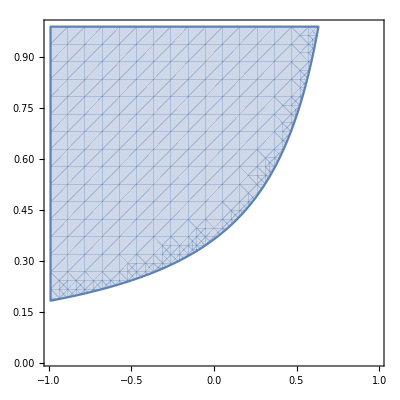

```mathematica
RegionPlot[1/(1-r)<m≤4/(3-3 r)||4/3+m r<m||((4+3 m (-1+r)) (4+11 m (-1+r))<0&&m≤1+m r), {r, -0.99,0.99},{m,0.01,0.99}]
```

```mathematica
Reduce[{1/(1-r)<m≤4/(3-3 r)||4/3+m r<m||((4+3 m (-1+r)) (4+11 m (-1+r))<0&&m≤1+m r)},m]
```

(r<1&&m>-4/(-11+11 r))||(r>1&&(m<-4/(-3+3 r)||-1/(-1+r)≤m<-4/(-11+11 r)))

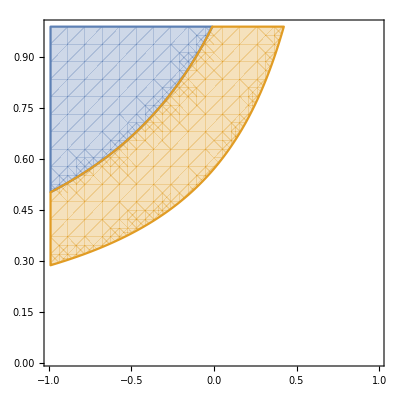

```mathematica
RegionPlot[{m(1-r)>1,(k<(m-m r)/((4+3 m (-1+r)) θ^2)&&m≤1+m r)/.{θ-> 1/2, k-> 1}},{r, -0.99,0.99},{m,0.01,0.99}]
```

```mathematica
RegionPlot[{m(1-r)>1,(4k θ^2/(1+3k θ^2)<m(1-r)<1)/.{θ-> 1/2, k-> 1}},{r, -0.99,0.99},{m,0.01,0.99}]
```

-Graphics-

### Polymorphic ESS This part is an unsuccessful attempt to provide analytical insights in the case of two residents in the populations.

#### Definitions

ni = 3 types are competing (2 residents, 1 invading mutant). The two residents are at traits z_1 and z_2=1-z_1

```mathematica
ni=3; 
Do[
Subscript[dn, i,1]=(Subscript[b, 1][Subscript[z, i]](1-m)-∑_(j=1)^ni Subscript[n, j,1])Subscript[n, i,1]+1/2 m ((1-r)Subscript[b, 2][Subscript[z, i]] Subscript[n, i,2]+(1+r)Subscript[b, 1][Subscript[z, i]] Subscript[n, i,1]);
Subscript[dn, i,2]=(Subscript[b, 2][Subscript[z, i]](1-m)-∑_(j=1)^ni Subscript[n, j,2])Subscript[n, i,2]+1/2 m ((1-r)Subscript[b, 1][Subscript[z, i]] Subscript[n, i,1]+(1+r)Subscript[b, 2][Subscript[z, i]] Subscript[n, i,2]);,{i,1,ni}]
```

Symmetry for the residents

```mathematica
sr3=Flatten[{Subscript[n, 1,1]->n11R,Subscript[n, 1,2]->n12R,Subscript[n, 2,1]->n12R,Subscript[n, 2,2]->n11R,Subscript[n, 3,1]->0,Subscript[n, 3,2]->0}];
```

#### Calculation of the invasion condition

```mathematica
M3=({{D[Subscript[dn, 3,1],Subscript[n, 3,1]], D[Subscript[dn, 3,1],Subscript[n, 3,2]]}, {D[Subscript[dn, 3,2],Subscript[n, 3,1]], D[Subscript[dn, 3,2],Subscript[n, 3,2]]}})/.sr3
```

{{-n11R-n12R+(1-m) (1-k (θ+z_3)^2)+1/2 m (1+r) (1-k (θ+z_3)^2),1/2 m (1-r) (1-k (-θ+z_3)^2)},{1/2 m (1-r) (1-k (θ+z_3)^2),-n11R-n12R+(1-m) (1-k (-θ+z_3)^2)+1/2 m (1+r) (1-k (-θ+z_3)^2)}}

```mathematica
EV3=Eigenvalues[M3]
λm3=AF[pc,EV3⟦2⟧]
```

{1/2 (2-m-2 n11R-2 n12R+m r-2 k θ^2+k m θ^2-k m r θ^2-2 k z_3^2+k m z_3^2-k m r z_3^2-√(m^2-2 m^2 r+m^2 r^2-2 k m^2 θ^2+4 k m^2 r θ^2-2 k m^2 r^2 θ^2+k^2 m^2 θ^4-2 k^2 m^2 r θ^4+k^2 m^2 r^2 θ^4-2 k m^2 z_3^2+4 k m^2 r z_3^2-2 k m^2 r^2 z_3^2+16 k^2 θ^2 z_3^2-16 k^2 m θ^2 z_3^2+2 k^2 m^2 θ^2 z_3^2+16 k^2 m r θ^2 z_3^2-4 k^2 m^2 r θ^2 z_3^2+2 k^2 m^2 r^2 θ^2 z_3^2+k^2 m^2 z_3^4-2 k^2 m^2 r z_3^4+k^2 m^2 r^2 z_3^4)),1/2 (2-m-2 n11R-2 n12R+m r-2 k θ^2+k m θ^2-k m r θ^2-2 k z_3^2+k m z_3^2-k m r z_3^2+√(m^2-2 m^2 r+m^2 r^2-2 k m^2 θ^2+4 k m^2 r θ^2-2 k m^2 r^2 θ^2+k^2 m^2 θ^4-2 k^2 m^2 r θ^4+k^2 m^2 r^2 θ^4-2 k m^2 z_3^2+4 k m^2 r z_3^2-2 k m^2 r^2 z_3^2+16 k^2 θ^2 z_3^2-16 k^2 m θ^2 z_3^2+2 k^2 m^2 θ^2 z_3^2+16 k^2 m r θ^2 z_3^2-4 k^2 m^2 r θ^2 z_3^2+2 k^2 m^2 r^2 θ^2 z_3^2+k^2 m^2 z_3^4-2 k^2 m^2 r z_3^4+k^2 m^2 r^2 z_3^4))}

1/2 (-m (-1+r) (-1+k θ^2+k z_3^2)-2 (-1+n11R+n12R+k θ^2+k z_3^2)+√(m^2 (-1+r)^2 (-1+k θ^2)^2+k z_3^2 (-2 m^2 (-1+r)^2+2 k (8+m (8+m (-1+r)) (-1+r)) θ^2+k m^2 (-1+r)^2 z_3^2)))

#### Selection gradient

Attention : the equilibrium of the resident depends on its trait z_1 and also on m and g

```mathematica
pc = {p>0&&θ∈Reals&&θ>0&&r∈Reals&&r>-1&&r<1&&m>0&&m<1&&m∈Reals&&Subscript[z, 1]∈Reals&&Subscript[z, 2]∈Reals&&k∈Reals&& k>0 && Subscript[z, 1]>0}
```

{p>0&&θ∈ℝ&&θ>0&&r∈ℝ&&r>-1&&r<1&&m>0&&m<1&&m∈ℝ&&z_1∈ℝ&&z_2∈ℝ&&k∈ℝ&&k>0&&z_1>0}

```mathematica
nr={n11R->n11[Subscript[z, 1]],n12R->n12[Subscript[z, 1]]};
Dλ3=AF[pc,D[λm3/.nr,Subscript[z, 3]]/.Subscript[z, 3]->Subscript[z, 1]]
```

k z_1 (-2+m-m r+(8 k θ^2+m (-1+r) (m-m r+k (8+m (-1+r)) θ^2)+k m^2 (-1+r)^2 z_1^2)/(√(m^2 (-1+r)^2 (-1+k θ^2)^2+k z_1^2 (-2 m^2 (-1+r)^2+2 k (8+m (8+m (-1+r)) (-1+r)) θ^2+k m^2 (-1+r)^2 z_1^2))))

```mathematica
solDim =AF[pc,Solve[Dλ3==0,Subscript[z, 1]]]
eqpoly=%⟦2⟧;
```

{{z_1→0},{z_1→-√(1/(m^2 (k+k m (-1+r)) (-1+r)^2)(-(1+m (-1+r)) (8 k θ^2+m (-1+r) (m-m r+k (8+m (-1+r)) θ^2))+2 (-2+m-m r) θ √(k (-m^2 (-1+r)^2+k (2+m (-1+r))^2 θ^2)) Abs[1+m (-1+r)]))},{z_1→√(1/(m^2 (k+k m (-1+r)) (-1+r)^2)(-(1+m (-1+r)) (8 k θ^2+m (-1+r) (m-m r+k (8+m (-1+r)) θ^2))+2 (-2+m-m r) θ √(k (-m^2 (-1+r)^2+k (2+m (-1+r))^2 θ^2)) Abs[1+m (-1+r)]))},{z_1→-√(1/(m^2 (k+k m (-1+r)) (-1+r)^2)(-(1+m (-1+r)) (8 k θ^2+m (-1+r) (m-m r+k (8+m (-1+r)) θ^2))+2 (2+m (-1+r)) θ √(k (-m^2 (-1+r)^2+k (2+m (-1+r))^2 θ^2)) Abs[1+m (-1+r)]))},{z_1→√(1/(m^2 (k+k m (-1+r)) (-1+r)^2)(-(1+m (-1+r)) (8 k θ^2+m (-1+r) (m-m r+k (8+m (-1+r)) θ^2))+2 (2+m (-1+r)) θ √(k (-m^2 (-1+r)^2+k (2+m (-1+r))^2 θ^2)) Abs[1+m (-1+r)]))}}

```mathematica
solDim⟦5⟧⟦1⟧⟦2⟧/.{m->0.6, r-> 0., k -> 1,  θ -> 1/2}
```

0.+0.264695 ⅈ

```mathematica
Factor[AF[pc && m(1-r)>1,solDim⟦5⟧⟦1⟧⟦2⟧/.θ->1/2 /.k-> 1]^2]
```

1/(4 m^2 (-1+r)^2)(-8+8 m+3 m^2-4 √(4-m (-4+3 m (-1+r)) (-1+r))+2 m √(4-m (-4+3 m (-1+r)) (-1+r))-8 m r-6 m^2 r-2 m √(4-m (-4+3 m (-1+r)) (-1+r)) r+3 m^2 r^2)

### Persistence of two types

```mathematica
ni=2; 
Do[
Subscript[dn, i,1]=(Subscript[b, 1][Subscript[z, i]](1-m)-∑_(j=1)^ni Subscript[n, j,1])Subscript[n, i,1]+1/2 m ((1-r)Subscript[b, 2][Subscript[z, i]] Subscript[n, i,2]+(1+r)Subscript[b, 1][Subscript[z, i]] Subscript[n, i,1]);
Subscript[dn, i,2]=(Subscript[b, 2][Subscript[z, i]](1-m)-∑_(j=1)^ni Subscript[n, j,2])Subscript[n, i,2]+1/2 m ((1-r)Subscript[b, 1][Subscript[z, i]] Subscript[n, i,1]+(1+r)Subscript[b, 2][Subscript[z, i]] Subscript[n, i,2]);,{i,1,ni}]
```

General equilibrium

```mathematica
symtwotypes = {Subscript[n, 1,2]-> Subscript[n, 2,1], Subscript[n, 2,2]-> Subscript[n, 1,1],Subscript[z, 2]-> -Subscript[z, 1]};
eq0 = {AF[pc,Subscript[dn, 1,1] /.symtwotypes /. ]==0 ,AF[pc,Subscript[dn, 2,1]/.symtwotypes]==0  }
AF[pc ,Solve[eq0,{Subscript[n, 1,1], Subscript[n, 2,1]}]]
```

\Beta Diversity

```mathematica
β = FullSimplify[1/2((solDim⟦4⟧⟦1⟧⟦2⟧)^2 + (solDim⟦5⟧⟦1⟧⟦2⟧)^2)]
```

1/(m^2 (k+k m (-1+r)) (-1+r)^2)(-(1+m (-1+r)) (8 k θ^2+m (-1+r) (m-m r+k (8+m (-1+r)) θ^2))+2 (2+m (-1+r)) θ √(k (-m^2 (-1+r)^2+k (2+m (-1+r))^2 θ^2)) Abs[1+m (-1+r)])

```mathematica
β /.{m->0.5, r-> -0.5, k -> 0.5,  θ -> 1}
```

0.384168

```mathematica
β /.{ r-> 0, k ->1,  θ -> 1}
```

(-(8-8 m) (1-m)+2 (2-m) √((2-m)^2-m^2) Abs[1-m])/((1-m) m^2)

```mathematica
FullSimplify[(-(8-16 m) (1-2 m)+2 (2-2 m) √((2-2 m)^2-4 m^2) Abs[1-2 m])/(4 (1-2 m) m^2)]
```

(2 ((1-2 m)^2+√(1-2 m) (-1+m) Abs[1-2 m]))/(m^2 (-1+2 m))

E Stability

```mathematica
ESλ3=AF[pc,D[λm3/.nr,Subscript[z, 3],Subscript[z, 3]]/.Subscript[z, 3]->Subscript[z, 1]/.eqpoly]
AF[pc,Reduce[ESλ3<0]]
```

(k m^4 (2+m (-1+r)) (-1+r)^4 θ-k^2 m^2 (2+m (-1+r))^3 (-1+r)^2 θ^3+4 k^(3/2) (1+m (-1+r)) (8+m (8+m (-1+r)) (-1+r)) θ^2 √(-m^2 (-1+r)^2+k (2+m (-1+r))^2 θ^2)-4 m^2 (1+m (-1+r)) (-1+r)^2 √(k (-m^2 (-1+r)^2+k (2+m (-1+r))^2 θ^2)))/(-m^4 (-1+r)^4 θ+k m^2 (2+m (-1+r))^2 (-1+r)^2 θ^3)-(k (2+m (-1+r)) (-8+m (-8+m (-1+r)) (-1+r)))/(m^2 (-1+r)^2 Sign[1+m (-1+r)])

Reduce::infc: The system (k m^4 (2+m Plus[«2»]) (-1+r)^4 θ-k^2 m^2 (2+Times[«2»])^3 (-1+r)^2 θ^3+4 k^(3/2) (1+m Plus[«2»]) (8+m Plus[«2»] Plus[«2»]) θ^2 √(Times[«3»]+Times[«3»])-4 m^2 (1+m Plus[«2»]) (-1+r)^2 √(k Plus[«2»]))/(-m^4 Plus[«2»]^4 θ+k m^2 Plus[«2»]^2 Plus[«2»]^2 θ^3)-(k (2+m (-1+r)) (-8+m (-8+m Plus[«2»]) (-1+r)))/(m^2 (-1+r)^2 Sign[1+m Plus[«2»]])<0 contains an infinite object ComplexInfinity.

$Aborted